```mathematica
PartitionType[sets_]:=Sort[Map[Length[#]&,sets],#1>#2&]
```

```mathematica
PartitionType2[s_]:=PartitionType[SymbolToSets[s]]
```

```mathematica
PartitionTypeLabel[p_]:=StringJoin[ Map[ToString[#]&,p]]
```

```mathematica
Graph [{1,2,3},{}]
```

-Graphics-

```mathematica
Map[PartitionType2[#]&,FindFullFormula[Graph [{1,2,3},{}]]]
```

{{1,1,1},{2,1},{2,1},{2,1},{3}}

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[prefix<>StringDrop[SymbolName[s],1]]
```

```mathematica
repFiveT=Table[ChangeSymbol[allGraphs5[k,"colofour"],"n"]->PartitionType2[allGraphs5[k,"colofour"]],{k,allGraphs5AtomKeys}]
```

{n1x2x3x4x5→{1,1,1,1,1},n1x2x3x45→{2,1,1,1},n1x2x35x4→{2,1,1,1},n1x2x34x5→{2,1,1,1},n1x2x345→{3,1,1},n1x25x3x4→{2,1,1,1},n1x25x34→{2,2,1},n1x24x3x5→{2,1,1,1},n1x24x35→{2,2,1},n1x245x3→{3,1,1},n1x23x4x5→{2,1,1,1},n1x23x45→{2,2,1},n1x235x4→{3,1,1},n1x234x5→{3,1,1},n1x2345→{4,1},n15x2x3x4→{2,1,1,1},n15x2x34→{2,2,1},n15x24x3→{2,2,1},n15x23x4→{2,2,1},n15x234→{3,2},n14x2x3x5→{2,1,1,1},n14x2x35→{2,2,1},n14x25x3→{2,2,1},n14x23x5→{2,2,1},n14x235→{3,2},n145x2x3→{3,1,1},n145x23→{3,2},n13x2x4x5→{2,1,1,1},n13x2x45→{2,2,1},n13x25x4→{2,2,1},n13x24x5→{2,2,1},n13x245→{3,2},n135x2x4→{3,1,1},n135x24→{3,2},n134x2x5→{3,1,1},n134x25→{3,2},n1345x2→{4,1},n12x3x4x5→{2,1,1,1},n12x3x45→{2,2,1},n12x35x4→{2,2,1},n12x34x5→{2,2,1},n12x345→{3,2},n125x3x4→{3,1,1},n125x34→{3,2},n124x3x5→{3,1,1},n124x35→{3,2},n1245x3→{4,1},n123x4x5→{3,1,1},n123x45→{3,2},n1235x4→{4,1},n1234x5→{4,1},n12345→{5}}

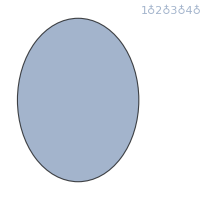

```mathematica
FormulaGraph[allGraphs5[0,"colofourrealnull"]]
```

```mathematica
DeleteDuplicates[ListofVars[allGraphs5[K5Key,"colofourrealnull"]]/.repFiveT]
```

{{2,2,1},{1,1,1,1,1},{5},{4,1},{3,2},{3,1,1},{2,1,1,1}}

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[prefix<>StringDrop[SymbolName[s],1]]
```

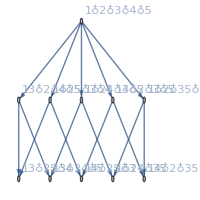

```mathematica
FormulaGraph[allGraphs5[lambdaKey,"colofour"]]
```

```mathematica
repFiveT=Table[ChangeSymbol[allGraphs5[k,"colofour"],"v"]->PartitionType2[allGraphs5[k,"colofour"]],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5→{1,1,1,1,1},v1x2x3x45→{2,1,1,1},v1x2x35x4→{2,1,1,1},v1x2x34x5→{2,1,1,1},v1x2x345→{3,1,1},v1x25x3x4→{2,1,1,1},v1x25x34→{2,2,1},v1x24x3x5→{2,1,1,1},v1x24x35→{2,2,1},v1x245x3→{3,1,1},v1x23x4x5→{2,1,1,1},v1x23x45→{2,2,1},v1x235x4→{3,1,1},v1x234x5→{3,1,1},v1x2345→{4,1},v15x2x3x4→{2,1,1,1},v15x2x34→{2,2,1},v15x24x3→{2,2,1},v15x23x4→{2,2,1},v15x234→{3,2},v14x2x3x5→{2,1,1,1},v14x2x35→{2,2,1},v14x25x3→{2,2,1},v14x23x5→{2,2,1},v14x235→{3,2},v145x2x3→{3,1,1},v145x23→{3,2},v13x2x4x5→{2,1,1,1},v13x2x45→{2,2,1},v13x25x4→{2,2,1},v13x24x5→{2,2,1},v13x245→{3,2},v135x2x4→{3,1,1},v135x24→{3,2},v134x2x5→{3,1,1},v134x25→{3,2},v1345x2→{4,1},v12x3x4x5→{2,1,1,1},v12x3x45→{2,2,1},v12x35x4→{2,2,1},v12x34x5→{2,2,1},v12x345→{3,2},v125x3x4→{3,1,1},v125x34→{3,2},v124x3x5→{3,1,1},v124x35→{3,2},v1245x3→{4,1},v123x4x5→{3,1,1},v123x45→{3,2},v1235x4→{4,1},v1234x5→{4,1},v12345→{5}}

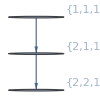

```mathematica
Graph[DeleteDuplicates[EdgeList[FormulaGraph[allGraphs5[lambdaKey,"colofour"]]]/.repFiveT],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->{100,100}]
```

```mathematica
Graph[DeleteDuplicates[EdgeList[FormulaGraph[allGraphs5[amigo1,"colofour"]]]/.repFiveT],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->{100,100}]
```

-Graphics-

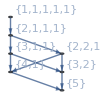

```mathematica
Graph[DeleteDuplicates[EdgeList[FormulaGraph[allGraphs5[0,"colofour"]]]/.repFiveT],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->{100,100}]
```

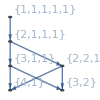
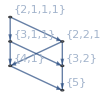
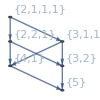
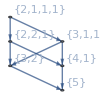
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[Table[Graph[DeleteDuplicates[EdgeList[FormulaGraph[allGraphs5[k,"colofour"]]]/.repFiveT],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->{100,100}],{k,child}],{child,allGraphs5[0,"children"]}]
```

```mathematica
Graph[DeleteDuplicates[EdgeList[FormulaGraph[allGraphs5[27226,"colofour"]]]/.repFiveT],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->{100,100}]
```

-Graphics-

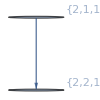

```mathematica
Graph[DeleteDuplicates[EdgeList[FormulaGraph[allGraphs5[35977,"colofour"]]]/.repFiveT],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->{100,100}]
```

```mathematica
Graph[DeleteDuplicates[EdgeList[FormulaGraph[allGraphs5[alfaKey,"colofour"]]]/.repFiveT],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->{100,100}]
```

-Graphics-

```mathematica
Graph[EdgeList[FormulaGraph[allGraphs5[K5Key,"colofourrealnull"]]]/.repFiveT//DeleteDuplicates,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

-Graphics-

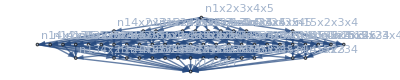

```mathematica
Graph[EdgeList[MobiusGraph5[K5Key,allGraphs5]]/.repFiveT//DeleteDuplicates,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

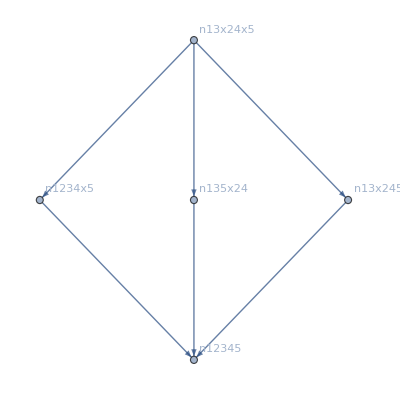

```mathematica
Graph[EdgeList[MobiusGraph5[alfa1Key,allGraphs5]]/.repFiveT//DeleteDuplicates,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

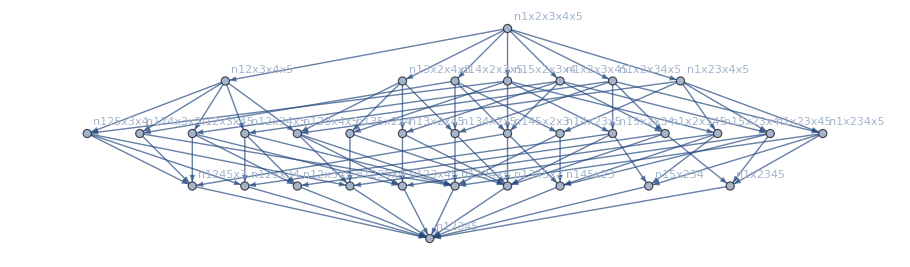

```mathematica
Graph[EdgeList[MobiusGraph5[amigo1,allGraphs5]]/.repFiveT//DeleteDuplicates,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
PartitionType2[n124x3x5]//PartitionTypeLabel
```

311

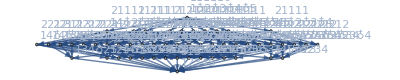

```mathematica
With[
{g=MobiusGraph5[K5Key,allGraphs5]},
Graph[EdgeList[g],VertexLabels->Table[k->Column[{
Framed[Row[{Style[PartitionTypeLabel[PartitionType2[k]],Red],Style[VertexInDegree[g,k],Bold]}],Background->White],
SymbolToLabel[k]
}],{k,VertexList[g]}],
GraphLayout->"LayeredDigraphEmbedding"]
]
```

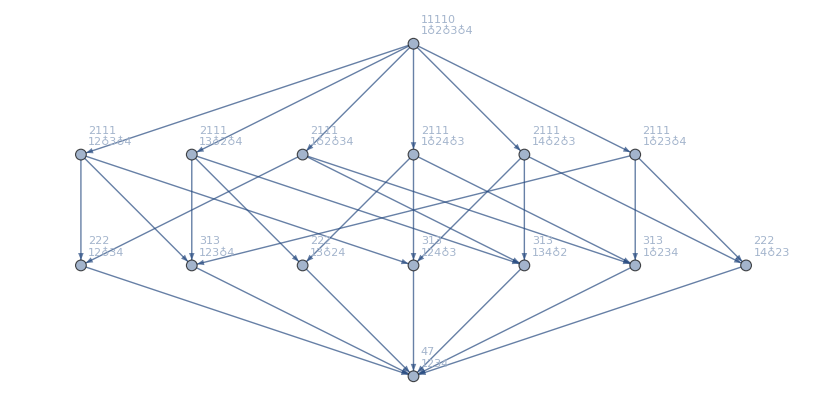

```mathematica
With[
{g=MobiusGraph4[K4Key,allGraphs4]},
Graph[EdgeList[g],VertexLabels->Table[k->Column[{
Framed[Row[{Style[PartitionTypeLabel[PartitionType2[k]],Red],Style[VertexInDegree[g,k],Bold]}],Background->White],
SymbolToLabel[k]
}],{k,VertexList[g]}],
GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
StirlingS2[2,2]
```

1

## Six does the same

```mathematica
repSixT=Table[allGraphs6[k,"colofourrealnull"]->PartitionType2[allGraphs6[k,"colofourrealnull"]],{k,allGraphs6NullAtomKeys}];
```

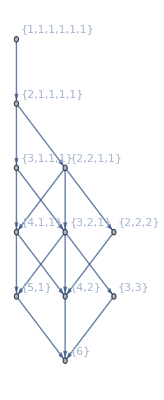

```mathematica
Graph[EdgeList[MobiusGraph5[K6Key,allGraphs6]]/.repSixT//DeleteDuplicates,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
FormulaGraph[allGraphs5[K5Key,"colofour"]]
```

-Graphics-

```mathematica
PartitionTypeToSymbol[s_, prefix_:"t"]:=Symbol[prefix<>StringRiffle[Map[IntegerString[#,36]&,s],"x"]]
```

```mathematica
PartitionTypeToSymbol[PartitionType2[allGraphs5[K5Key,"colofour"]],"t"]
```

t1x1x1x1x1

## Lets do it for 5

```mathematica
RepFul5=Table[allGraphs5[k,"colofour"]->PartitionTypeToSymbol[PartitionType2[allGraphs5[k,"colofour"]],"t"],{k,allGraphs5AtomKeys}]
```

```mathematica
RepFul5Chrom=Table[PartitionTypeToSymbol[PartitionType2[allGraphs5[k,"colofour"]],"t"] ->ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5AtomKeys}]
```

{t1x1x1x1x1→24 x-50 x^2+35 x^3-10 x^4+x^5,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t3x1x1→2 x-3 x^2+x^3,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x2x1→2 x-3 x^2+x^3,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x2x1→2 x-3 x^2+x^3,t3x1x1→2 x-3 x^2+x^3,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x2x1→2 x-3 x^2+x^3,t3x1x1→2 x-3 x^2+x^3,t3x1x1→2 x-3 x^2+x^3,t4x1→-x+x^2,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x2x1→2 x-3 x^2+x^3,t2x2x1→2 x-3 x^2+x^3,t2x2x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x2x1→2 x-3 x^2+x^3,t2x2x1→2 x-3 x^2+x^3,t2x2x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t3x1x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x2x1→2 x-3 x^2+x^3,t2x2x1→2 x-3 x^2+x^3,t2x2x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t3x1x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t3x1x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t4x1→-x+x^2,t2x1x1x1→-6 x+11 x^2-6 x^3+x^4,t2x2x1→2 x-3 x^2+x^3,t2x2x1→2 x-3 x^2+x^3,t2x2x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t3x1x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t3x1x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t4x1→-x+x^2,t3x1x1→2 x-3 x^2+x^3,t3x2→-x+x^2,t4x1→-x+x^2,t4x1→-x+x^2,t5→x}

```mathematica
Table[allGraphs5[k,"colofour"]/.RepFul5,{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]//DeleteDuplicates//Sort//TableForm
```

t1x1x1x1x1
t1x1x1x1x1+t2x1x1x1
t1x1x1x1x1+2 t2x1x1x1
t1x1x1x1x1+3 t2x1x1x1
t1x1x1x1x1+4 t2x1x1x1
t1x1x1x1x1+2 t2x1x1x1+t2x2x1
t1x1x1x1x1+3 t2x1x1x1+t2x2x1
t1x1x1x1x1+3 t2x1x1x1+2 t2x2x1
t1x1x1x1x1+4 t2x1x1x1+2 t2x2x1
t1x1x1x1x1+4 t2x1x1x1+3 t2x2x1
t1x1x1x1x1+5 t2x1x1x1+4 t2x2x1
t1x1x1x1x1+5 t2x1x1x1+5 t2x2x1
t1x1x1x1x1+6 t2x1x1x1+6 t2x2x1
t1x1x1x1x1+3 t2x1x1x1+t3x1x1
t1x1x1x1x1+4 t2x1x1x1+t2x2x1+t3x1x1
t1x1x1x1x1+5 t2x1x1x1+2 t2x2x1+t3x1x1
t1x1x1x1x1+5 t2x1x1x1+3 t2x2x1+t3x1x1
t1x1x1x1x1+5 t2x1x1x1+2 t2x2x1+2 t3x1x1
t1x1x1x1x1+6 t2x1x1x1+4 t2x2x1+2 t3x1x1
t1x1x1x1x1+7 t2x1x1x1+6 t2x2x1+3 t3x1x1
t1x1x1x1x1+4 t2x1x1x1+3 t2x2x1+t3x1x1+t3x2
t1x1x1x1x1+5 t2x1x1x1+4 t2x2x1+t3x1x1+t3x2
t1x1x1x1x1+6 t2x1x1x1+6 t2x2x1+t3x1x1+t3x2
t1x1x1x1x1+6 t2x1x1x1+5 t2x2x1+2 t3x1x1+t3x2
t1x1x1x1x1+6 t2x1x1x1+5 t2x2x1+2 t3x1x1+2 t3x2
t1x1x1x1x1+7 t2x1x1x1+8 t2x2x1+2 t3x1x1+2 t3x2
t1x1x1x1x1+7 t2x1x1x1+7 t2x2x1+3 t3x1x1+2 t3x2
t1x1x1x1x1+8 t2x1x1x1+10 t2x2x1+4 t3x1x1+4 t3x2
t1x1x1x1x1+6 t2x1x1x1+3 t2x2x1+4 t3x1x1+t4x1
t1x1x1x1x1+7 t2x1x1x1+6 t2x2x1+4 t3x1x1+t3x2+t4x1
t1x1x1x1x1+8 t2x1x1x1+9 t2x2x1+5 t3x1x1+3 t3x2+t4x1
t1x1x1x1x1+9 t2x1x1x1+12 t2x2x1+7 t3x1x1+6 t3x2+2 t4x1
t1x1x1x1x1+10 t2x1x1x1+15 t2x2x1+10 t3x1x1+10 t3x2+5 t4x1+t5

```mathematica
Table[(allGraphs5[k,"colofour"]/.RepNul5 /.RepNul5Chrom),{k,Select[Keys[allGraphs5]//Simplify,VertexCount[allGraphs5[#,"graph"]]==5&]}]//DeleteDuplicates//Sort//TableForm
```

```mathematica
RepNul5=Table[allGraphs5[k,"colofourrealnull"]->PartitionTypeToSymbol[PartitionType2[allGraphs5[k,"colofourrealnull"]],"t"],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5→t1x1x1x1x1,n12x3x4x5→t2x1x1x1,n123x4x5→t3x1x1,n1234x5→t4x1,n12345→t5,n1235x4→t4x1,n123x45→t3x2,n124x3x5→t3x1x1,n1245x3→t4x1,n124x35→t3x2,n125x3x4→t3x1x1,n125x34→t3x2,n12x34x5→t2x2x1,n12x345→t3x2,n12x35x4→t2x2x1,n12x3x45→t2x2x1,n13x2x4x5→t2x1x1x1,n134x2x5→t3x1x1,n1345x2→t4x1,n134x25→t3x2,n135x2x4→t3x1x1,n135x24→t3x2,n13x24x5→t2x2x1,n13x245→t3x2,n13x25x4→t2x2x1,n13x2x45→t2x2x1,n14x2x3x5→t2x1x1x1,n145x2x3→t3x1x1,n145x23→t3x2,n14x23x5→t2x2x1,n14x235→t3x2,n14x25x3→t2x2x1,n14x2x35→t2x2x1,n15x2x3x4→t2x1x1x1,n15x23x4→t2x2x1,n15x234→t3x2,n15x24x3→t2x2x1,n15x2x34→t2x2x1,n1x23x4x5→t2x1x1x1,n1x234x5→t3x1x1,n1x2345→t4x1,n1x235x4→t3x1x1,n1x23x45→t2x2x1,n1x24x3x5→t2x1x1x1,n1x245x3→t3x1x1,n1x24x35→t2x2x1,n1x25x3x4→t2x1x1x1,n1x25x34→t2x2x1,n1x2x34x5→t2x1x1x1,n1x2x345→t3x1x1,n1x2x35x4→t2x1x1x1,n1x2x3x45→t2x1x1x1}

```mathematica
RepNul5Chrom=Table[PartitionTypeToSymbol[PartitionType2[allGraphs5[k,"colofourrealnull"]],"t"] ->ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5NullAtomKeys}]
```

{t1x1x1x1x1→x^5,t2x1x1x1→x^4,t3x1x1→x^3,t4x1→x^2,t5→x,t4x1→x^2,t3x2→x^2,t3x1x1→x^3,t4x1→x^2,t3x2→x^2,t3x1x1→x^3,t3x2→x^2,t2x2x1→x^3,t3x2→x^2,t2x2x1→x^3,t2x2x1→x^3,t2x1x1x1→x^4,t3x1x1→x^3,t4x1→x^2,t3x2→x^2,t3x1x1→x^3,t3x2→x^2,t2x2x1→x^3,t3x2→x^2,t2x2x1→x^3,t2x2x1→x^3,t2x1x1x1→x^4,t3x1x1→x^3,t3x2→x^2,t2x2x1→x^3,t3x2→x^2,t2x2x1→x^3,t2x2x1→x^3,t2x1x1x1→x^4,t2x2x1→x^3,t3x2→x^2,t2x2x1→x^3,t2x2x1→x^3,t2x1x1x1→x^4,t3x1x1→x^3,t4x1→x^2,t3x1x1→x^3,t2x2x1→x^3,t2x1x1x1→x^4,t3x1x1→x^3,t2x2x1→x^3,t2x1x1x1→x^4,t2x2x1→x^3,t2x1x1x1→x^4,t3x1x1→x^3,t2x1x1x1→x^4,t2x1x1x1→x^4}

```mathematica
Table[(allGraphs5[k,"colofourrealnull"]/.RepNul5 /.RepNul5Chrom),{k,Select[Keys[allGraphs5]//Simplify,VertexCount[allGraphs5[#,"graph"]]==5&]}]//DeleteDuplicates//Sort//TableForm
```

x^5
24 x-50 x^2+35 x^3-10 x^4+x^5
18 x-39 x^2+29 x^3-9 x^4+x^5
12 x-28 x^2+23 x^3-8 x^4+x^5
14 x-31 x^2+24 x^3-8 x^4+x^5
6 x-17 x^2+17 x^3-7 x^4+x^5
8 x-20 x^2+18 x^3-7 x^4+x^5
10 x-23 x^2+19 x^3-7 x^4+x^5
-6 x^2+11 x^3-6 x^4+x^5
4 x-12 x^2+13 x^3-6 x^4+x^5
6 x-15 x^2+14 x^3-6 x^4+x^5
7 x-17 x^2+15 x^3-6 x^4+x^5
-4 x^2+8 x^3-5 x^4+x^5
2 x-7 x^2+9 x^3-5 x^4+x^5
4 x-10 x^2+10 x^3-5 x^4+x^5
3 x-9 x^2+10 x^3-5 x^4+x^5
-2 x^2+5 x^3-4 x^4+x^5
x-4 x^2+6 x^3-4 x^4+x^5
-3 x^2+6 x^3-4 x^4+x^5
2 x^3-3 x^4+x^5
-x^2+3 x^3-3 x^4+x^5
x^3-2 x^4+x^5
-x^4+x^5

## Lets do it for 6

```mathematica
RepFul6=Table[allGraphs6[k,"colofour"]->PartitionTypeToSymbol[PartitionType2[allGraphs6[k,"colofour"]],"t"],{k,allGraphs6AtomKeys}]
```

{v1x2x3x4x5x6→t1x1x1x1x1x1,v1x2x3x4x56→t2x1x1x1x1,v1x2x3x46x5→t2x1x1x1x1,v1x2x3x45x6→t2x1x1x1x1,v1x2x3x456→t3x1x1x1,v1x2x36x4x5→t2x1x1x1x1,v1x2x36x45→t2x2x1x1,v1x2x35x4x6→t2x1x1x1x1,v1x2x35x46→t2x2x1x1,v1x2x356x4→t3x1x1x1,v1x2x34x5x6→t2x1x1x1x1,v1x2x34x56→t2x2x1x1,v1x2x346x5→t3x1x1x1,v1x2x345x6→t3x1x1x1,v1x2x3456→t4x1x1,v1x26x3x4x5→t2x1x1x1x1,v1x26x3x45→t2x2x1x1,v1x26x35x4→t2x2x1x1,v1x26x34x5→t2x2x1x1,v1x26x345→t3x2x1,v1x25x3x4x6→t2x1x1x1x1,v1x25x3x46→t2x2x1x1,v1x25x36x4→t2x2x1x1,v1x25x34x6→t2x2x1x1,v1x25x346→t3x2x1,v1x256x3x4→t3x1x1x1,v1x256x34→t3x2x1,v1x24x3x5x6→t2x1x1x1x1,v1x24x3x56→t2x2x1x1,v1x24x36x5→t2x2x1x1,v1x24x35x6→t2x2x1x1,v1x24x356→t3x2x1,v1x246x3x5→t3x1x1x1,v1x246x35→t3x2x1,v1x245x3x6→t3x1x1x1,v1x245x36→t3x2x1,v1x2456x3→t4x1x1,v1x23x4x5x6→t2x1x1x1x1,v1x23x4x56→t2x2x1x1,v1x23x46x5→t2x2x1x1,v1x23x45x6→t2x2x1x1,v1x23x456→t3x2x1,v1x236x4x5→t3x1x1x1,v1x236x45→t3x2x1,v1x235x4x6→t3x1x1x1,v1x235x46→t3x2x1,v1x2356x4→t4x1x1,v1x234x5x6→t3x1x1x1,v1x234x56→t3x2x1,v1x2346x5→t4x1x1,v1x2345x6→t4x1x1,v1x23456→t5x1,v16x2x3x4x5→t2x1x1x1x1,v16x2x3x45→t2x2x1x1,v16x2x35x4→t2x2x1x1,v16x2x34x5→t2x2x1x1,v16x2x345→t3x2x1,v16x25x3x4→t2x2x1x1,v16x25x34→t2x2x2,v16x24x3x5→t2x2x1x1,v16x24x35→t2x2x2,v16x245x3→t3x2x1,v16x23x4x5→t2x2x1x1,v16x23x45→t2x2x2,v16x235x4→t3x2x1,v16x234x5→t3x2x1,v16x2345→t4x2,v15x2x3x4x6→t2x1x1x1x1,v15x2x3x46→t2x2x1x1,v15x2x36x4→t2x2x1x1,v15x2x34x6→t2x2x1x1,v15x2x346→t3x2x1,v15x26x3x4→t2x2x1x1,v15x26x34→t2x2x2,v15x24x3x6→t2x2x1x1,v15x24x36→t2x2x2,v15x246x3→t3x2x1,v15x23x4x6→t2x2x1x1,v15x23x46→t2x2x2,v15x236x4→t3x2x1,v15x234x6→t3x2x1,v15x2346→t4x2,v156x2x3x4→t3x1x1x1,v156x2x34→t3x2x1,v156x24x3→t3x2x1,v156x23x4→t3x2x1,v156x234→t3x3,v14x2x3x5x6→t2x1x1x1x1,v14x2x3x56→t2x2x1x1,v14x2x36x5→t2x2x1x1,v14x2x35x6→t2x2x1x1,v14x2x356→t3x2x1,v14x26x3x5→t2x2x1x1,v14x26x35→t2x2x2,v14x25x3x6→t2x2x1x1,v14x25x36→t2x2x2,v14x256x3→t3x2x1,v14x23x5x6→t2x2x1x1,v14x23x56→t2x2x2,v14x236x5→t3x2x1,v14x235x6→t3x2x1,v14x2356→t4x2,v146x2x3x5→t3x1x1x1,v146x2x35→t3x2x1,v146x25x3→t3x2x1,v146x23x5→t3x2x1,v146x235→t3x3,v145x2x3x6→t3x1x1x1,v145x2x36→t3x2x1,v145x26x3→t3x2x1,v145x23x6→t3x2x1,v145x236→t3x3,v1456x2x3→t4x1x1,v1456x23→t4x2,v13x2x4x5x6→t2x1x1x1x1,v13x2x4x56→t2x2x1x1,v13x2x46x5→t2x2x1x1,v13x2x45x6→t2x2x1x1,v13x2x456→t3x2x1,v13x26x4x5→t2x2x1x1,v13x26x45→t2x2x2,v13x25x4x6→t2x2x1x1,v13x25x46→t2x2x2,v13x256x4→t3x2x1,v13x24x5x6→t2x2x1x1,v13x24x56→t2x2x2,v13x246x5→t3x2x1,v13x245x6→t3x2x1,v13x2456→t4x2,v136x2x4x5→t3x1x1x1,v136x2x45→t3x2x1,v136x25x4→t3x2x1,v136x24x5→t3x2x1,v136x245→t3x3,v135x2x4x6→t3x1x1x1,v135x2x46→t3x2x1,v135x26x4→t3x2x1,v135x24x6→t3x2x1,v135x246→t3x3,v1356x2x4→t4x1x1,v1356x24→t4x2,v134x2x5x6→t3x1x1x1,v134x2x56→t3x2x1,v134x26x5→t3x2x1,v134x25x6→t3x2x1,v134x256→t3x3,v1346x2x5→t4x1x1,v1346x25→t4x2,v1345x2x6→t4x1x1,v1345x26→t4x2,v13456x2→t5x1,v12x3x4x5x6→t2x1x1x1x1,v12x3x4x56→t2x2x1x1,v12x3x46x5→t2x2x1x1,v12x3x45x6→t2x2x1x1,v12x3x456→t3x2x1,v12x36x4x5→t2x2x1x1,v12x36x45→t2x2x2,v12x35x4x6→t2x2x1x1,v12x35x46→t2x2x2,v12x356x4→t3x2x1,v12x34x5x6→t2x2x1x1,v12x34x56→t2x2x2,v12x346x5→t3x2x1,v12x345x6→t3x2x1,v12x3456→t4x2,v126x3x4x5→t3x1x1x1,v126x3x45→t3x2x1,v126x35x4→t3x2x1,v126x34x5→t3x2x1,v126x345→t3x3,v125x3x4x6→t3x1x1x1,v125x3x46→t3x2x1,v125x36x4→t3x2x1,v125x34x6→t3x2x1,v125x346→t3x3,v1256x3x4→t4x1x1,v1256x34→t4x2,v124x3x5x6→t3x1x1x1,v124x3x56→t3x2x1,v124x36x5→t3x2x1,v124x35x6→t3x2x1,v124x356→t3x3,v1246x3x5→t4x1x1,v1246x35→t4x2,v1245x3x6→t4x1x1,v1245x36→t4x2,v12456x3→t5x1,v123x4x5x6→t3x1x1x1,v123x4x56→t3x2x1,v123x46x5→t3x2x1,v123x45x6→t3x2x1,v123x456→t3x3,v1236x4x5→t4x1x1,v1236x45→t4x2,v1235x4x6→t4x1x1,v1235x46→t4x2,v12356x4→t5x1,v1234x5x6→t4x1x1,v1234x56→t4x2,v12346x5→t5x1,v12345x6→t5x1,v123456→t6}

```mathematica
parts=Sort[Table[PartitionTypeToSymbol[PartitionType2[allGraphs6[k,"colofour"]],"t"] ,{k,allGraphs6AtomKeys}]//DeleteDuplicates, CompareSymbols]
```

{t1x1x1x1x1x1,t2x1x1x1x1,t2x2x1x1,t2x2x2,t3x1x1x1,t3x2x1,t3x3,t4x1x1,t4x2,t5x1,t6}

```mathematica
PartCoeff[poly_]:=Table[Coefficient[poly,k],{k,parts}]
```

```mathematica
RepFul6Chrom=Table[PartitionTypeToSymbol[PartitionType2[allGraphs6[k,"colofour"]],"t"] ->ChromaticPolynomial[allGraphs6[k,"graph"],x],{k,allGraphs6AtomKeys}];
```

```mathematica
MatrixRank[Table[PartCoeff[allGraphs6[k,"colofour"]/.RepFul6],{k,allGraphs6NullAtomKeys}]]
```

11

```mathematica
matFull=Table[PartCoeff[allGraphs6[k,"colofour"]/.RepFul6],{k,allGraphs6NullAtomKeys}]//DeleteDuplicates//Sort
```

{{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,1,1,2,1},{0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,1,1,0,1,1,1},{0,0,0,0,1,3,1,3,3,3,1},{0,0,0,1,0,0,0,0,3,0,1},{0,0,1,1,0,4,2,1,3,2,1},{0,1,6,3,4,16,4,6,7,4,1},{1,15,45,15,20,60,10,15,15,6,1}}

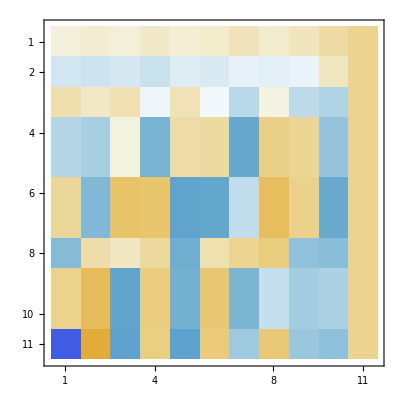

```mathematica
Eigenvectors[matFull]//N//MatrixPlot
```

```mathematica
MatrixForm[matFull,TableHeadings->{Map[SymbolToLabel[#]&,Table[allGraphs6[m,"colofourrealnull"],{m,allGraphs6NullAtomKeys}]],Map[Rotate[ SymbolToLabel[#],Pi/2]&,parts]}]
```

( | 1♁1♁1♁1♁1♁1 | 2♁1♁1♁1♁1 | 2♁2♁1♁1 | 2♁2♁2 | 3♁1♁1♁1 | 3♁2♁1 | 3♁3 | 4♁1♁1 | 4♁2 | 5♁1 | 6
1♁2♁3♁4♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
12♁3♁4♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
123♁4♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1234♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 1
12345♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
123456 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1
12346♁5 | 0 | 0 | 0 | 0 | 1 | 3 | 1 | 3 | 3 | 3 | 1
1234♁56 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 0 | 1
1235♁4♁6 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 1 | 3 | 2 | 1
12356♁4 | 0 | 1 | 6 | 3 | 4 | 16 | 4 | 6 | 7 | 4 | 1
1235♁46 | 1 | 15 | 45 | 15 | 20 | 60 | 10 | 15 | 15 | 6 | 1)

```mathematica
Det[%434]
```

-1

```mathematica
parts5=Sort[Table[PartitionTypeToSymbol[PartitionType2[allGraphs5[k,"colofourrealnull"]],"t"] ,{k,allGraphs5NullAtomKeys}]//DeleteDuplicates, CompareSymbols]
```

{t1x1x1x1x1,t2x1x1x1,t2x2x1,t3x1x1,t3x2,t4x1,t5}

```mathematica
Part5Coeff2[poly_]:=Table[Coefficient[poly,k],{k,parts5}]
```

```mathematica
mat15=Table[Part5Coeff2[allGraphs5[k,"colofourrealnull"]/.RepNul5],{k,allGraphs5AtomKeys}]//DeleteDuplicates//Sort
```

{{0,0,0,0,0,0,1},{0,0,0,0,0,1,-1},{0,0,0,0,1,0,-1},{0,0,0,1,-1,-2,2},{0,0,1,0,-2,-1,2},{0,1,-3,-3,5,6,-6},{1,-10,15,20,-20,-30,24}}

```mathematica
MatrixForm[mat15,
 TableHeadings->{Map[SymbolToLabel[#]&,Table[allGraphs5[m,"colofour"],{m,allGraphs5AtomKeys}]],Map[Rotate[ SymbolToLabel[#],Pi/2]&,parts5]}, TableSpacing->{2,2}]
```

( | 1♁1♁1♁1♁1 | 2♁1♁1♁1 | 2♁2♁1 | 3♁1♁1 | 3♁2 | 4♁1 | 5
1♁2♁3♁4♁5 | 1 | -10 | 15 | 20 | -20 | -30 | 24
1♁2♁3♁45 | 0 | 1 | -3 | -3 | 5 | 6 | -6
1♁2♁35♁4 | 0 | 0 | 1 | 0 | -2 | -1 | 2
1♁2♁34♁5 | 0 | 0 | 0 | 1 | -1 | -2 | 2
1♁2♁345 | 0 | 0 | 0 | 0 | 1 | 0 | -1
1♁25♁3♁4 | 0 | 0 | 0 | 0 | 0 | 1 | -1
1♁25♁34 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Total[{1,-10, 15, 20,-20,-30 ,24}]
```

0

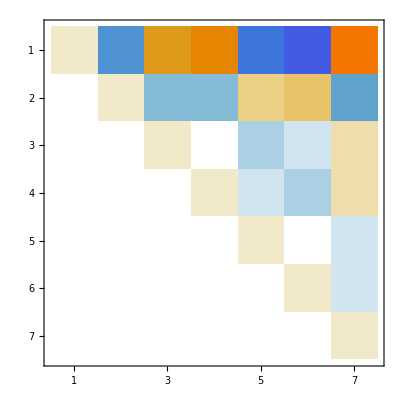

```mathematica
MatrixPlot[mat15]
```

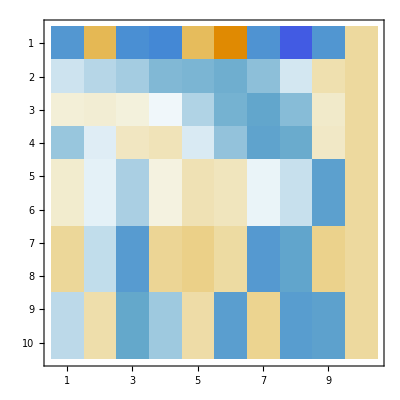

```mathematica
Table[IntegerPartitions[n,k]//Length,{n,1,10},{k,1,10}]//Eigenvectors//N//MatrixPlot
```

```mathematica
parts2=Sort[Table[PartitionTypeToSymbol[PartitionType2[allGraphs6[k,"colofourrealnull"]],"t"] ,{k,allGraphs6NullAtomKeys}]//DeleteDuplicates, CompareSymbols]
```

{t1x1x1x1x1x1,t2x1x1x1x1,t2x2x1x1,t2x2x2,t3x1x1x1,t3x2x1,t3x3,t4x1x1,t4x2,t5x1,t6}

```mathematica
PartCoeff2[poly_]:=Table[Coefficient[poly,k],{k,parts2}]
```

```mathematica
mat1=Table[PartCoeff2[allGraphs6[k,"colofourrealnull"]/.RepNul6],{k,allGraphs6AtomKeys}]//DeleteDuplicates//ReverseSort;
```

```mathematica
MatrixForm[mat1,
 TableHeadings->{Map[SymbolToLabel[#]&,Table[allGraphs6[m,"colofour"],{m,allGraphs6AtomKeys}]],Map[Rotate[ SymbolToLabel[#],Pi/2]&,parts]}, TableSpacing->{2,2}]
```

( | 1♁1♁1♁1♁1♁1 | 2♁1♁1♁1♁1 | 2♁2♁1♁1 | 2♁2♁2 | 3♁1♁1♁1 | 3♁2♁1 | 3♁3 | 4♁1♁1 | 4♁2 | 5♁1 | 6
1♁2♁3♁4♁5♁6 | 1 | -15 | 45 | -15 | 40 | -120 | 40 | -90 | 90 | 144 | -120
1♁2♁3♁4♁56 | 0 | 1 | -6 | 3 | -4 | 20 | -8 | 12 | -18 | -24 | 24
1♁2♁3♁46♁5 | 0 | 0 | 1 | -1 | 0 | -4 | 2 | -1 | 5 | 4 | -6
1♁2♁3♁45♁6 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -3 | 0 | 2
1♁2♁3♁456 | 0 | 0 | 0 | 0 | 1 | -3 | 2 | -3 | 3 | 6 | -6
1♁2♁36♁4♁5 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | -1 | 2
1♁2♁36♁45 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
1♁2♁35♁4♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -2 | 2
1♁2♁35♁46 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
1♁2♁356♁4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
1♁2♁34♁5♁6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
mat1//Total
```

{1,-14,40,-12,37,-106,36,-81,76,128,-104}

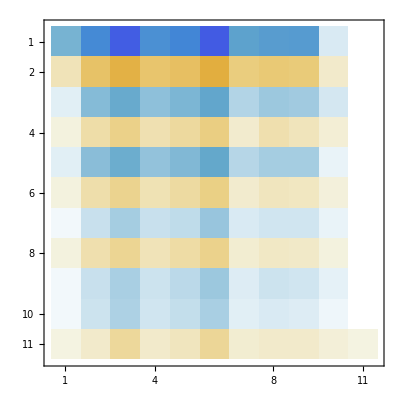

```mathematica
mat1.matFull//MatrixPlot
```

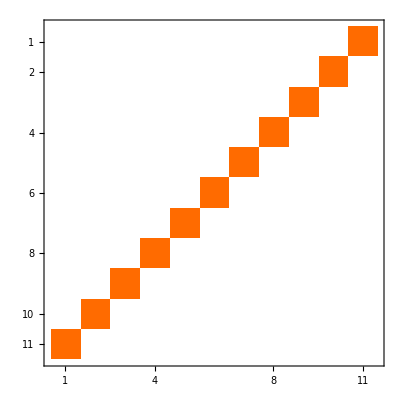

```mathematica
matFull.mat1//MatrixPlot
```

```mathematica
matFull//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 3 | 1 | 3 | 3 | 3 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 0 | 1
0 | 0 | 1 | 1 | 0 | 4 | 2 | 1 | 3 | 2 | 1
0 | 1 | 6 | 3 | 4 | 16 | 4 | 6 | 7 | 4 | 1
1 | 15 | 45 | 15 | 20 | 60 | 10 | 15 | 15 | 6 | 1)

```mathematica
mat1.PartCoeff2[allGraphs6[3,"colofourrealnull"]/.RepNul6]
```

{16,-1,0,0,0,0,0,0,0,0,0}

```mathematica
PartCoeff[allGraphs6[3,"colofour"]/.RepFul6]
```

{1,14,39,12,16,44,6,9,8,2,0}

```mathematica
Det[%443]
```

-1

```mathematica
MatrixForm[Table[PartCoeff[allGraphs6[k,"colofour"]/.RepFul6],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}]//DeleteDuplicates//Sort,TableHeadings->{None,Map[Rotate[ SymbolToLabel[#],Pi/2]&,parts]}]
```

(1♁1♁1♁1♁1♁1 | 2♁1♁1♁1♁1 | 2♁2♁1♁1 | 2♁2♁2 | 3♁1♁1♁1 | 3♁2♁1 | 3♁3 | 4♁1♁1 | 4♁2 | 5♁1 | 6
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 3 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 4 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 5 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 5 | 6 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 5 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 5 | 6 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 3 | 0 | 4 | 0 | 0 | 1 | 0 | 0 | 0
1 | 6 | 4 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 5 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
1 | 6 | 5 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0
1 | 6 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 6 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 6 | 6 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 6 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 6 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 7 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 6 | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 7 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 6 | 7 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0
1 | 6 | 8 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 8 | 1 | 1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 6 | 8 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | 9 | 0 | 2 | 6 | 1 | 0 | 0 | 0 | 0
1 | 6 | 9 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 7 | 6 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
1 | 7 | 6 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
1 | 7 | 6 | 0 | 4 | 1 | 0 | 1 | 0 | 0 | 0
1 | 7 | 7 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
1 | 7 | 7 | 0 | 3 | 2 | 0 | 0 | 0 | 0 | 0
1 | 7 | 7 | 1 | 2 | 2 | 0 | 0 | 0 | 0 | 0
1 | 7 | 8 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0
1 | 7 | 8 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0
1 | 7 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 7 | 9 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 7 | 9 | 1 | 2 | 2 | 0 | 0 | 0 | 0 | 0
1 | 7 | 9 | 1 | 2 | 3 | 0 | 0 | 0 | 0 | 0
1 | 7 | 9 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0
1 | 7 | 9 | 3 | 4 | 4 | 0 | 1 | 1 | 0 | 0
1 | 7 | 10 | 1 | 1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 7 | 10 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 7 | 10 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 7 | 10 | 2 | 1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 7 | 10 | 2 | 2 | 3 | 0 | 0 | 0 | 0 | 0
1 | 7 | 11 | 1 | 2 | 6 | 1 | 0 | 0 | 0 | 0
1 | 7 | 11 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 7 | 11 | 2 | 1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 7 | 11 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 8 | 9 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
1 | 8 | 9 | 0 | 4 | 2 | 0 | 1 | 0 | 0 | 0
1 | 8 | 9 | 0 | 5 | 3 | 0 | 1 | 0 | 0 | 0
1 | 8 | 10 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0
1 | 8 | 10 | 1 | 3 | 2 | 0 | 0 | 0 | 0 | 0
1 | 8 | 10 | 1 | 4 | 2 | 0 | 1 | 0 | 0 | 0
1 | 8 | 11 | 1 | 3 | 3 | 0 | 0 | 0 | 0 | 0
1 | 8 | 11 | 2 | 3 | 2 | 0 | 0 | 0 | 0 | 0
1 | 8 | 11 | 2 | 3 | 4 | 0 | 0 | 0 | 0 | 0
1 | 8 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 8 | 12 | 1 | 2 | 3 | 0 | 0 | 0 | 0 | 0
1 | 8 | 12 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0
1 | 8 | 12 | 2 | 3 | 4 | 0 | 0 | 0 | 0 | 0
1 | 8 | 12 | 3 | 4 | 5 | 0 | 1 | 1 | 0 | 0
1 | 8 | 13 | 2 | 1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 8 | 13 | 2 | 2 | 4 | 0 | 0 | 0 | 0 | 0
1 | 8 | 13 | 2 | 3 | 7 | 1 | 0 | 0 | 0 | 0
1 | 8 | 13 | 3 | 2 | 3 | 0 | 0 | 0 | 0 | 0
1 | 8 | 14 | 2 | 2 | 6 | 1 | 0 | 0 | 0 | 0
1 | 8 | 14 | 3 | 1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 8 | 14 | 3 | 2 | 4 | 0 | 0 | 0 | 0 | 0
1 | 8 | 14 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 9 | 12 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
1 | 9 | 12 | 0 | 7 | 6 | 0 | 2 | 0 | 0 | 0
1 | 9 | 13 | 1 | 5 | 4 | 0 | 1 | 0 | 0 | 0
1 | 9 | 14 | 2 | 4 | 4 | 0 | 0 | 0 | 0 | 0
1 | 9 | 14 | 2 | 5 | 5 | 0 | 1 | 0 | 0 | 0
1 | 9 | 15 | 2 | 4 | 6 | 0 | 0 | 0 | 0 | 0
1 | 9 | 15 | 3 | 4 | 6 | 0 | 0 | 0 | 0 | 0
1 | 9 | 15 | 3 | 5 | 7 | 0 | 1 | 1 | 0 | 0
1 | 9 | 15 | 3 | 5 | 9 | 1 | 1 | 1 | 0 | 0
1 | 9 | 16 | 2 | 2 | 4 | 0 | 0 | 0 | 0 | 0
1 | 9 | 16 | 3 | 3 | 5 | 0 | 0 | 0 | 0 | 0
1 | 9 | 16 | 3 | 4 | 8 | 1 | 0 | 0 | 0 | 0
1 | 9 | 16 | 4 | 3 | 4 | 0 | 0 | 0 | 0 | 0
1 | 9 | 16 | 4 | 4 | 6 | 0 | 1 | 1 | 0 | 0
1 | 9 | 17 | 3 | 3 | 8 | 1 | 0 | 0 | 0 | 0
1 | 9 | 17 | 4 | 2 | 4 | 0 | 0 | 0 | 0 | 0
1 | 9 | 17 | 4 | 3 | 6 | 0 | 0 | 0 | 0 | 0
1 | 9 | 18 | 4 | 2 | 6 | 1 | 0 | 0 | 0 | 0
1 | 9 | 18 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 10 | 15 | 0 | 10 | 10 | 0 | 5 | 0 | 1 | 0
1 | 10 | 17 | 2 | 6 | 6 | 0 | 1 | 0 | 0 | 0
1 | 10 | 17 | 2 | 7 | 8 | 0 | 2 | 0 | 0 | 0
1 | 10 | 18 | 3 | 6 | 8 | 0 | 1 | 0 | 0 | 0
1 | 10 | 18 | 3 | 7 | 10 | 0 | 2 | 1 | 0 | 0
1 | 10 | 19 | 4 | 5 | 8 | 0 | 0 | 0 | 0 | 0
1 | 10 | 19 | 4 | 6 | 10 | 1 | 1 | 0 | 0 | 0
1 | 10 | 19 | 4 | 6 | 11 | 1 | 1 | 1 | 0 | 0
1 | 10 | 20 | 4 | 4 | 8 | 0 | 0 | 0 | 0 | 0
1 | 10 | 20 | 4 | 5 | 11 | 1 | 0 | 0 | 0 | 0
1 | 10 | 20 | 5 | 5 | 9 | 0 | 1 | 1 | 0 | 0
1 | 10 | 20 | 5 | 5 | 10 | 0 | 0 | 0 | 0 | 0
1 | 10 | 21 | 4 | 4 | 12 | 2 | 0 | 0 | 0 | 0
1 | 10 | 21 | 5 | 4 | 10 | 1 | 0 | 0 | 0 | 0
1 | 10 | 21 | 6 | 3 | 6 | 0 | 0 | 0 | 0 | 0
1 | 11 | 21 | 3 | 10 | 14 | 0 | 5 | 1 | 1 | 0
1 | 11 | 22 | 4 | 8 | 12 | 0 | 2 | 0 | 0 | 0
1 | 11 | 23 | 5 | 8 | 15 | 1 | 2 | 1 | 0 | 0
1 | 11 | 23 | 5 | 8 | 16 | 2 | 2 | 2 | 0 | 0
1 | 11 | 24 | 6 | 6 | 12 | 0 | 0 | 0 | 0 | 0
1 | 11 | 24 | 6 | 7 | 14 | 0 | 2 | 2 | 0 | 0
1 | 11 | 24 | 6 | 7 | 15 | 1 | 1 | 1 | 0 | 0
1 | 11 | 25 | 6 | 6 | 16 | 2 | 0 | 0 | 0 | 0
1 | 11 | 25 | 7 | 6 | 14 | 1 | 1 | 1 | 0 | 0
1 | 12 | 27 | 6 | 10 | 18 | 0 | 3 | 0 | 0 | 0
1 | 12 | 27 | 6 | 11 | 21 | 1 | 5 | 2 | 1 | 0
1 | 12 | 28 | 7 | 10 | 22 | 2 | 3 | 2 | 0 | 0
1 | 12 | 29 | 8 | 9 | 22 | 2 | 2 | 2 | 0 | 0
1 | 12 | 30 | 8 | 8 | 24 | 4 | 0 | 0 | 0 | 0
1 | 13 | 33 | 9 | 13 | 31 | 3 | 6 | 4 | 1 | 0
1 | 13 | 34 | 10 | 12 | 32 | 4 | 4 | 4 | 0 | 0
1 | 14 | 39 | 12 | 16 | 44 | 6 | 9 | 8 | 2 | 0
1 | 15 | 45 | 15 | 20 | 60 | 10 | 15 | 15 | 6 | 1)

```mathematica
IntegerPartitions[6]//Length
```

11

```mathematica
Table[allGraphs6[k,"colofour"]/.RepFul6,{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}]//DeleteDuplicates//Sort//TableForm
```

t1x1x1x1x1x1
t1x1x1x1x1x1+t2x1x1x1x1
t1x1x1x1x1x1+2 t2x1x1x1x1
t1x1x1x1x1x1+3 t2x1x1x1x1
t1x1x1x1x1x1+4 t2x1x1x1x1
t1x1x1x1x1x1+5 t2x1x1x1x1
t1x1x1x1x1x1+2 t2x1x1x1x1+t2x2x1x1
t1x1x1x1x1x1+3 t2x1x1x1x1+t2x2x1x1
t1x1x1x1x1x1+3 t2x1x1x1x1+2 t2x2x1x1
t1x1x1x1x1x1+4 t2x1x1x1x1+2 t2x2x1x1
t1x1x1x1x1x1+4 t2x1x1x1x1+3 t2x2x1x1
t1x1x1x1x1x1+5 t2x1x1x1x1+3 t2x2x1x1
t1x1x1x1x1x1+4 t2x1x1x1x1+4 t2x2x1x1
t1x1x1x1x1x1+5 t2x1x1x1x1+4 t2x2x1x1
t1x1x1x1x1x1+5 t2x1x1x1x1+5 t2x2x1x1
t1x1x1x1x1x1+6 t2x1x1x1x1+6 t2x2x1x1
t1x1x1x1x1x1+6 t2x1x1x1x1+7 t2x2x1x1
t1x1x1x1x1x1+7 t2x1x1x1x1+9 t2x2x1x1
t1x1x1x1x1x1+8 t2x1x1x1x1+12 t2x2x1x1
t1x1x1x1x1x1+3 t2x1x1x1x1+3 t2x2x1x1+t2x2x2
t1x1x1x1x1x1+4 t2x1x1x1x1+4 t2x2x1x1+t2x2x2
t1x1x1x1x1x1+5 t2x1x1x1x1+5 t2x2x1x1+t2x2x2
t1x1x1x1x1x1+5 t2x1x1x1x1+6 t2x2x1x1+t2x2x2
t1x1x1x1x1x1+6 t2x1x1x1x1+7 t2x2x1x1+t2x2x2
t1x1x1x1x1x1+6 t2x1x1x1x1+8 t2x2x1x1+t2x2x2
t1x1x1x1x1x1+5 t2x1x1x1x1+6 t2x2x1x1+2 t2x2x2
t1x1x1x1x1x1+6 t2x1x1x1x1+8 t2x2x1x1+2 t2x2x2
t1x1x1x1x1x1+6 t2x1x1x1x1+9 t2x2x1x1+2 t2x2x2
t1x1x1x1x1x1+7 t2x1x1x1x1+10 t2x2x1x1+2 t2x2x2
t1x1x1x1x1x1+7 t2x1x1x1x1+11 t2x2x1x1+2 t2x2x2
t1x1x1x1x1x1+7 t2x1x1x1x1+11 t2x2x1x1+3 t2x2x2
t1x1x1x1x1x1+8 t2x1x1x1x1+14 t2x2x1x1+4 t2x2x2
t1x1x1x1x1x1+9 t2x1x1x1x1+18 t2x2x1x1+6 t2x2x2
t1x1x1x1x1x1+3 t2x1x1x1x1+t3x1x1x1
t1x1x1x1x1x1+4 t2x1x1x1x1+t2x2x1x1+t3x1x1x1
t1x1x1x1x1x1+5 t2x1x1x1x1+2 t2x2x1x1+t3x1x1x1
t1x1x1x1x1x1+5 t2x1x1x1x1+3 t2x2x1x1+t3x1x1x1
t1x1x1x1x1x1+6 t2x1x1x1x1+3 t2x2x1x1+t3x1x1x1
t1x1x1x1x1x1+6 t2x1x1x1x1+5 t2x2x1x1+t3x1x1x1
t1x1x1x1x1x1+6 t2x1x1x1x1+6 t2x2x1x1+t2x2x2+t3x1x1x1
t1x1x1x1x1x1+5 t2x1x1x1x1+2 t2x2x1x1+2 t3x1x1x1
t1x1x1x1x1x1+6 t2x1x1x1x1+4 t2x2x1x1+2 t3x1x1x1
t1x1x1x1x1x1+7 t2x1x1x1x1+6 t2x2x1x1+2 t3x1x1x1
t1x1x1x1x1x1+7 t2x1x1x1x1+7 t2x2x1x1+2 t3x1x1x1
t1x1x1x1x1x1+7 t2x1x1x1x1+6 t2x2x1x1+3 t3x1x1x1
t1x1x1x1x1x1+8 t2x1x1x1x1+9 t2x2x1x1+3 t3x1x1x1
t1x1x1x1x1x1+9 t2x1x1x1x1+12 t2x2x1x1+4 t3x1x1x1
t1x1x1x1x1x1+4 t2x1x1x1x1+3 t2x2x1x1+t3x1x1x1+t3x2x1
t1x1x1x1x1x1+5 t2x1x1x1x1+4 t2x2x1x1+t3x1x1x1+t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+6 t2x2x1x1+t3x1x1x1+t3x2x1
t1x1x1x1x1x1+5 t2x1x1x1x1+5 t2x2x1x1+t2x2x2+t3x1x1x1+t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+6 t2x2x1x1+t2x2x2+t3x1x1x1+t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+7 t2x2x1x1+t2x2x2+t3x1x1x1+t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+9 t2x2x1x1+t2x2x2+t3x1x1x1+t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+10 t2x2x1x1+2 t2x2x2+t3x1x1x1+t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+5 t2x2x1x1+2 t3x1x1x1+t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+8 t2x2x1x1+t2x2x2+2 t3x1x1x1+t3x2x1
t1x1x1x1x1x1+5 t2x1x1x1x1+6 t2x2x1x1+t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+7 t2x2x1x1+t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+8 t2x2x1x1+t2x2x2+t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+10 t2x2x1x1+t2x2x2+t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+10 t2x2x1x1+2 t2x2x2+t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+11 t2x2x1x1+2 t2x2x2+t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+13 t2x2x1x1+2 t2x2x2+t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+14 t2x2x1x1+3 t2x2x2+t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+5 t2x2x1x1+2 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+8 t2x2x1x1+2 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+7 t2x2x1x1+t2x2x2+2 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+9 t2x2x1x1+t2x2x2+2 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+7 t2x2x1x1+2 t2x2x2+2 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+9 t2x2x1x1+2 t2x2x2+2 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+12 t2x2x1x1+2 t2x2x2+2 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+7 t2x2x1x1+3 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+10 t2x2x1x1+t2x2x2+3 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+11 t2x2x1x1+2 t2x2x2+3 t3x1x1x1+2 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+9 t2x2x1x1+t2x2x2+2 t3x1x1x1+3 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+12 t2x2x1x1+t2x2x2+2 t3x1x1x1+3 t3x2x1
t1x1x1x1x1x1+7 t2x1x1x1x1+10 t2x2x1x1+2 t2x2x2+2 t3x1x1x1+3 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+13 t2x2x1x1+3 t2x2x2+2 t3x1x1x1+3 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+11 t2x2x1x1+t2x2x2+3 t3x1x1x1+3 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+13 t2x2x1x1+2 t2x2x2+2 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+9 t2x1x1x1x1+16 t2x2x1x1+2 t2x2x2+2 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+14 t2x2x1x1+3 t2x2x2+2 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+9 t2x1x1x1x1+17 t2x2x1x1+4 t2x2x2+2 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+11 t2x2x1x1+2 t2x2x2+3 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+12 t2x2x1x1+2 t2x2x2+3 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+9 t2x1x1x1x1+16 t2x2x1x1+4 t2x2x2+3 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+8 t2x1x1x1x1+10 t2x2x1x1+4 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+9 t2x1x1x1x1+14 t2x2x1x1+2 t2x2x2+4 t3x1x1x1+4 t3x2x1
t1x1x1x1x1x1+9 t2x1x1x1x1+16 t2x2x1x1+3 t2x2x2+3 t3x1x1x1+5 t3x2x1
t1x1x1x1x1x1+9 t2x1x1x1x1+17 t2x2x1x1+4 t2x2x2+3 t3x1x1x1+6 t3x2x1
t1x1x1x1x1x1+10 t2x1x1x1x1+21 t2x2x1x1+6 t2x2x2+3 t3x1x1x1+6 t3x2x1
t1x1x1x1x1x1+9 t2x1x1x1x1+15 t2x2x1x1+2 t2x2x2+4 t3x1x1x1+6 t3x2x1
t1x1x1x1x1x1+9 t2x1x1x1x1+15 t2x2x1x1+3 t2x2x2+4 t3x1x1x1+6 t3x2x1
t1x1x1x1x1x1+10 t2x1x1x1x1+20 t2x2x1x1+4 t2x2x2+4 t3x1x1x1+8 t3x2x1
t1x1x1x1x1x1+10 t2x1x1x1x1+19 t2x2x1x1+4 t2x2x2+5 t3x1x1x1+8 t3x2x1
t1x1x1x1x1x1+10 t2x1x1x1x1+20 t2x2x1x1+5 t2x2x2+5 t3x1x1x1+10 t3x2x1
t1x1x1x1x1x1+11 t2x1x1x1x1+24 t2x2x1x1+6 t2x2x2+6 t3x1x1x1+12 t3x2x1
t1x1x1x1x1x1+6 t2x1x1x1x1+9 t2x2x1x1+2 t3x1x1x1+6 t3x2x1+t3x3
t1x1x1x1x1x1+7 t2x1x1x1x1+11 t2x2x1x1+t2x2x2+2 t3x1x1x1+6 t3x2x1+t3x3
t1x1x1x1x1x1+8 t2x1x1x1x1+14 t2x2x1x1+2 t2x2x2+2 t3x1x1x1+6 t3x2x1+t3x3
t1x1x1x1x1x1+9 t2x1x1x1x1+18 t2x2x1x1+4 t2x2x2+2 t3x1x1x1+6 t3x2x1+t3x3
t1x1x1x1x1x1+8 t2x1x1x1x1+13 t2x2x1x1+2 t2x2x2+3 t3x1x1x1+7 t3x2x1+t3x3
t1x1x1x1x1x1+9 t2x1x1x1x1+17 t2x2x1x1+3 t2x2x2+3 t3x1x1x1+8 t3x2x1+t3x3
t1x1x1x1x1x1+9 t2x1x1x1x1+16 t2x2x1x1+3 t2x2x2+4 t3x1x1x1+8 t3x2x1+t3x3
t1x1x1x1x1x1+10 t2x1x1x1x1+21 t2x2x1x1+5 t2x2x2+4 t3x1x1x1+10 t3x2x1+t3x3
t1x1x1x1x1x1+10 t2x1x1x1x1+20 t2x2x1x1+4 t2x2x2+5 t3x1x1x1+11 t3x2x1+t3x3
t1x1x1x1x1x1+10 t2x1x1x1x1+21 t2x2x1x1+4 t2x2x2+4 t3x1x1x1+12 t3x2x1+2 t3x3
t1x1x1x1x1x1+11 t2x1x1x1x1+25 t2x2x1x1+6 t2x2x2+6 t3x1x1x1+16 t3x2x1+2 t3x3
t1x1x1x1x1x1+12 t2x1x1x1x1+30 t2x2x1x1+8 t2x2x2+8 t3x1x1x1+24 t3x2x1+4 t3x3
t1x1x1x1x1x1+6 t2x1x1x1x1+3 t2x2x1x1+4 t3x1x1x1+t4x1x1
t1x1x1x1x1x1+7 t2x1x1x1x1+6 t2x2x1x1+4 t3x1x1x1+t3x2x1+t4x1x1
t1x1x1x1x1x1+8 t2x1x1x1x1+9 t2x2x1x1+4 t3x1x1x1+2 t3x2x1+t4x1x1
t1x1x1x1x1x1+8 t2x1x1x1x1+10 t2x2x1x1+t2x2x2+4 t3x1x1x1+2 t3x2x1+t4x1x1
t1x1x1x1x1x1+8 t2x1x1x1x1+9 t2x2x1x1+5 t3x1x1x1+3 t3x2x1+t4x1x1
t1x1x1x1x1x1+9 t2x1x1x1x1+13 t2x2x1x1+t2x2x2+5 t3x1x1x1+4 t3x2x1+t4x1x1
t1x1x1x1x1x1+9 t2x1x1x1x1+14 t2x2x1x1+2 t2x2x2+5 t3x1x1x1+5 t3x2x1+t4x1x1
t1x1x1x1x1x1+10 t2x1x1x1x1+17 t2x2x1x1+2 t2x2x2+6 t3x1x1x1+6 t3x2x1+t4x1x1
t1x1x1x1x1x1+10 t2x1x1x1x1+18 t2x2x1x1+3 t2x2x2+6 t3x1x1x1+8 t3x2x1+t4x1x1
t1x1x1x1x1x1+10 t2x1x1x1x1+19 t2x2x1x1+4 t2x2x2+6 t3x1x1x1+10 t3x2x1+t3x3+t4x1x1
t1x1x1x1x1x1+9 t2x1x1x1x1+12 t2x2x1x1+7 t3x1x1x1+6 t3x2x1+2 t4x1x1
t1x1x1x1x1x1+10 t2x1x1x1x1+17 t2x2x1x1+2 t2x2x2+7 t3x1x1x1+8 t3x2x1+2 t4x1x1
t1x1x1x1x1x1+11 t2x1x1x1x1+22 t2x2x1x1+4 t2x2x2+8 t3x1x1x1+12 t3x2x1+2 t4x1x1
t1x1x1x1x1x1+12 t2x1x1x1x1+27 t2x2x1x1+6 t2x2x2+10 t3x1x1x1+18 t3x2x1+3 t4x1x1
t1x1x1x1x1x1+7 t2x1x1x1x1+9 t2x2x1x1+3 t2x2x2+4 t3x1x1x1+4 t3x2x1+t4x1x1+t4x2
t1x1x1x1x1x1+8 t2x1x1x1x1+12 t2x2x1x1+3 t2x2x2+4 t3x1x1x1+5 t3x2x1+t4x1x1+t4x2
t1x1x1x1x1x1+9 t2x1x1x1x1+16 t2x2x1x1+4 t2x2x2+4 t3x1x1x1+6 t3x2x1+t4x1x1+t4x2
t1x1x1x1x1x1+9 t2x1x1x1x1+15 t2x2x1x1+3 t2x2x2+5 t3x1x1x1+7 t3x2x1+t4x1x1+t4x2
t1x1x1x1x1x1+10 t2x1x1x1x1+20 t2x2x1x1+5 t2x2x2+5 t3x1x1x1+9 t3x2x1+t4x1x1+t4x2
t1x1x1x1x1x1+9 t2x1x1x1x1+15 t2x2x1x1+3 t2x2x2+5 t3x1x1x1+9 t3x2x1+t3x3+t4x1x1+t4x2
t1x1x1x1x1x1+10 t2x1x1x1x1+19 t2x2x1x1+4 t2x2x2+6 t3x1x1x1+11 t3x2x1+t3x3+t4x1x1+t4x2
t1x1x1x1x1x1+11 t2x1x1x1x1+25 t2x2x1x1+7 t2x2x2+6 t3x1x1x1+14 t3x2x1+t3x3+t4x1x1+t4x2
t1x1x1x1x1x1+11 t2x1x1x1x1+24 t2x2x1x1+6 t2x2x2+7 t3x1x1x1+15 t3x2x1+t3x3+t4x1x1+t4x2
t1x1x1x1x1x1+10 t2x1x1x1x1+18 t2x2x1x1+3 t2x2x2+7 t3x1x1x1+10 t3x2x1+2 t4x1x1+t4x2
t1x1x1x1x1x1+11 t2x1x1x1x1+23 t2x2x1x1+5 t2x2x2+8 t3x1x1x1+15 t3x2x1+t3x3+2 t4x1x1+t4x2
t1x1x1x1x1x1+11 t2x1x1x1x1+24 t2x2x1x1+6 t2x2x2+7 t3x1x1x1+14 t3x2x1+2 t4x1x1+2 t4x2
t1x1x1x1x1x1+11 t2x1x1x1x1+23 t2x2x1x1+5 t2x2x2+8 t3x1x1x1+16 t3x2x1+2 t3x3+2 t4x1x1+2 t4x2
t1x1x1x1x1x1+12 t2x1x1x1x1+29 t2x2x1x1+8 t2x2x2+9 t3x1x1x1+22 t3x2x1+2 t3x3+2 t4x1x1+2 t4x2
t1x1x1x1x1x1+12 t2x1x1x1x1+28 t2x2x1x1+7 t2x2x2+10 t3x1x1x1+22 t3x2x1+2 t3x3+3 t4x1x1+2 t4x2
t1x1x1x1x1x1+13 t2x1x1x1x1+34 t2x2x1x1+10 t2x2x2+12 t3x1x1x1+32 t3x2x1+4 t3x3+4 t4x1x1+4 t4x2
t1x1x1x1x1x1+10 t2x1x1x1x1+15 t2x2x1x1+10 t3x1x1x1+10 t3x2x1+5 t4x1x1+t5x1
t1x1x1x1x1x1+11 t2x1x1x1x1+21 t2x2x1x1+3 t2x2x2+10 t3x1x1x1+14 t3x2x1+5 t4x1x1+t4x2+t5x1
t1x1x1x1x1x1+12 t2x1x1x1x1+27 t2x2x1x1+6 t2x2x2+11 t3x1x1x1+21 t3x2x1+t3x3+5 t4x1x1+2 t4x2+t5x1
t1x1x1x1x1x1+13 t2x1x1x1x1+33 t2x2x1x1+9 t2x2x2+13 t3x1x1x1+31 t3x2x1+3 t3x3+6 t4x1x1+4 t4x2+t5x1
t1x1x1x1x1x1+14 t2x1x1x1x1+39 t2x2x1x1+12 t2x2x2+16 t3x1x1x1+44 t3x2x1+6 t3x3+9 t4x1x1+8 t4x2+2 t5x1
t1x1x1x1x1x1+15 t2x1x1x1x1+45 t2x2x1x1+15 t2x2x2+20 t3x1x1x1+60 t3x2x1+10 t3x3+15 t4x1x1+15 t4x2+6 t5x1+t6

```mathematica
Table[(allGraphs6[k,"colofour"]/.RepFul6 /.RepFul6Chrom),{k,Select[Keys[allGraphs6]//Simplify,VertexCount[allGraphs6[#,"graph"]]==6&]}]//DeleteDuplicates//Sort//TableForm
```

-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6
-96 x+224 x^2-190 x^3+75 x^4-14 x^5+x^6
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+2 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+3 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+3 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (-6 x+11 x^2-6 x^3+x^4)+3 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+3 (-6 x+11 x^2-6 x^3+x^4)+3 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+4 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-132 x+296 x^2-237 x^3+87 x^4-15 x^5+x^6+4 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (-6 x+11 x^2-6 x^3+x^4)+4 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+3 (-6 x+11 x^2-6 x^3+x^4)+4 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-124 x+282 x^2-230 x^3+86 x^4-15 x^5+x^6+3 (-6 x+11 x^2-6 x^3+x^4)+4 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+4 (-6 x+11 x^2-6 x^3+x^4)+4 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+4 (-6 x+11 x^2-6 x^3+x^4)+4 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+2 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+3 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+3 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+4 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-124 x+282 x^2-230 x^3+86 x^4-15 x^5+x^6+4 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+5 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+5 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-122 x+279 x^2-229 x^3+86 x^4-15 x^5+x^6+5 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+6 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+6 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+6 (-6 x+11 x^2-6 x^3+x^4)+5 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+3 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+5 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+6 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-124 x+282 x^2-230 x^3+86 x^4-15 x^5+x^6+6 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-122 x+279 x^2-229 x^3+86 x^4-15 x^5+x^6+6 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+7 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+7 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-122 x+279 x^2-229 x^3+86 x^4-15 x^5+x^6+7 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+7 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+7 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+8 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+8 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-124 x+282 x^2-230 x^3+86 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+8 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+9 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+4 (2 x-3 x^2+x^3)+9 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-121 x+275 x^2-225 x^3+85 x^4-15 x^5+x^6+6 (2 x-3 x^2+x^3)+11 (-6 x+11 x^2-6 x^3+x^4)+6 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+8 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+9 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-122 x+279 x^2-229 x^3+86 x^4-15 x^5+x^6+9 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+9 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-116 x+268 x^2-223 x^3+85 x^4-15 x^5+x^6+10 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+10 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-124 x+282 x^2-230 x^3+86 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+10 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+4 (2 x-3 x^2+x^3)+10 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+11 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+11 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+3 (2 x-3 x^2+x^3)+11 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+3 (2 x-3 x^2+x^3)+11 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+4 (2 x-3 x^2+x^3)+11 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+4 (2 x-3 x^2+x^3)+11 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+5 (2 x-3 x^2+x^3)+12 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-119 x+272 x^2-224 x^3+85 x^4-15 x^5+x^6+6 (2 x-3 x^2+x^3)+13 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-119 x+272 x^2-224 x^3+85 x^4-15 x^5+x^6+7 (2 x-3 x^2+x^3)+13 (-6 x+11 x^2-6 x^3+x^4)+7 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+12 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+13 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+4 (2 x-3 x^2+x^3)+13 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-116 x+268 x^2-223 x^3+85 x^4-15 x^5+x^6+2 (2 x-3 x^2+x^3)+14 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+3 (2 x-3 x^2+x^3)+14 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+4 (2 x-3 x^2+x^3)+14 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-126 x+285 x^2-231 x^3+86 x^4-15 x^5+x^6+5 (2 x-3 x^2+x^3)+14 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+6 (2 x-3 x^2+x^3)+14 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+6 (2 x-3 x^2+x^3)+15 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+7 (2 x-3 x^2+x^3)+16 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-121 x+275 x^2-225 x^3+85 x^4-15 x^5+x^6+8 (2 x-3 x^2+x^3)+16 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-119 x+272 x^2-224 x^3+85 x^4-15 x^5+x^6+8 (2 x-3 x^2+x^3)+16 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-121 x+275 x^2-225 x^3+85 x^4-15 x^5+x^6+9 (2 x-3 x^2+x^3)+16 (-6 x+11 x^2-6 x^3+x^4)+8 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+16 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-116 x+268 x^2-223 x^3+85 x^4-15 x^5+x^6+4 (2 x-3 x^2+x^3)+18 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+6 (2 x-3 x^2+x^3)+18 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+7 (2 x-3 x^2+x^3)+19 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+8 (2 x-3 x^2+x^3)+19 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+9 (2 x-3 x^2+x^3)+19 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+10 (2 x-3 x^2+x^3)+20 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-121 x+275 x^2-225 x^3+85 x^4-15 x^5+x^6+10 (2 x-3 x^2+x^3)+20 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-119 x+272 x^2-224 x^3+85 x^4-15 x^5+x^6+10 (2 x-3 x^2+x^3)+20 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-121 x+275 x^2-225 x^3+85 x^4-15 x^5+x^6+11 (2 x-3 x^2+x^3)+20 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+273 x^2-224 x^3+85 x^4-15 x^5+x^6+12 (2 x-3 x^2+x^3)+20 (-6 x+11 x^2-6 x^3+x^4)+9 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+8 (2 x-3 x^2+x^3)+23 (-6 x+11 x^2-6 x^3+x^4)+10 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-118 x+271 x^2-224 x^3+85 x^4-15 x^5+x^6+11 (2 x-3 x^2+x^3)+24 (-6 x+11 x^2-6 x^3+x^4)+10 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+12 (2 x-3 x^2+x^3)+24 (-6 x+11 x^2-6 x^3+x^4)+10 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-119 x+272 x^2-224 x^3+85 x^4-15 x^5+x^6+14 (2 x-3 x^2+x^3)+25 (-6 x+11 x^2-6 x^3+x^4)+10 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+15 (2 x-3 x^2+x^3)+25 (-6 x+11 x^2-6 x^3+x^4)+10 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-121 x+275 x^2-225 x^3+85 x^4-15 x^5+x^6+15 (2 x-3 x^2+x^3)+25 (-6 x+11 x^2-6 x^3+x^4)+10 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+273 x^2-224 x^3+85 x^4-15 x^5+x^6+15 (2 x-3 x^2+x^3)+25 (-6 x+11 x^2-6 x^3+x^4)+10 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (-x+x^2)+16 (2 x-3 x^2+x^3)+25 (-6 x+11 x^2-6 x^3+x^4)+10 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+18 (2 x-3 x^2+x^3)+30 (-6 x+11 x^2-6 x^3+x^4)+11 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+273 x^2-224 x^3+85 x^4-15 x^5+x^6+21 (2 x-3 x^2+x^3)+31 (-6 x+11 x^2-6 x^3+x^4)+11 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-122 x+276 x^2-225 x^3+85 x^4-15 x^5+x^6+22 (2 x-3 x^2+x^3)+31 (-6 x+11 x^2-6 x^3+x^4)+11 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (-x+x^2)+22 (2 x-3 x^2+x^3)+31 (-6 x+11 x^2-6 x^3+x^4)+11 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+4 (-x+x^2)+23 (2 x-3 x^2+x^3)+31 (-6 x+11 x^2-6 x^3+x^4)+11 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+27 (2 x-3 x^2+x^3)+37 (-6 x+11 x^2-6 x^3+x^4)+12 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-122 x+276 x^2-225 x^3+85 x^4-15 x^5+x^6+2 (-x+x^2)+32 (2 x-3 x^2+x^3)+38 (-6 x+11 x^2-6 x^3+x^4)+12 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+4 (-x+x^2)+32 (2 x-3 x^2+x^3)+38 (-6 x+11 x^2-6 x^3+x^4)+12 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-121 x+275 x^2-225 x^3+85 x^4-15 x^5+x^6+7 (-x+x^2)+46 (2 x-3 x^2+x^3)+46 (-6 x+11 x^2-6 x^3+x^4)+13 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+8 (-x+x^2)+46 (2 x-3 x^2+x^3)+46 (-6 x+11 x^2-6 x^3+x^4)+13 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+16 (-x+x^2)+65 (2 x-3 x^2+x^3)+55 (-6 x+11 x^2-6 x^3+x^4)+14 (24 x-50 x^2+35 x^3-10 x^4+x^5)
-119 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6+31 (-x+x^2)+90 (2 x-3 x^2+x^3)+65 (-6 x+11 x^2-6 x^3+x^4)+15 (24 x-50 x^2+35 x^3-10 x^4+x^5)

```mathematica
RepNul6=Table[allGraphs6[k,"colofourrealnull"]->PartitionTypeToSymbol[PartitionType2[allGraphs6[k,"colofourrealnull"]],"t"],{k,allGraphs6NullAtomKeys}]
```

{n1x2x3x4x5x6→t1x1x1x1x1x1,n12x3x4x5x6→t2x1x1x1x1,n123x4x5x6→t3x1x1x1,n1234x5x6→t4x1x1,n12345x6→t5x1,n123456→t6,n12346x5→t5x1,n1234x56→t4x2,n1235x4x6→t4x1x1,n12356x4→t5x1,n1235x46→t4x2,n1236x4x5→t4x1x1,n1236x45→t4x2,n123x45x6→t3x2x1,n123x456→t3x3,n123x46x5→t3x2x1,n123x4x56→t3x2x1,n124x3x5x6→t3x1x1x1,n1245x3x6→t4x1x1,n12456x3→t5x1,n1245x36→t4x2,n1246x3x5→t4x1x1,n1246x35→t4x2,n124x35x6→t3x2x1,n124x356→t3x3,n124x36x5→t3x2x1,n124x3x56→t3x2x1,n125x3x4x6→t3x1x1x1,n1256x3x4→t4x1x1,n1256x34→t4x2,n125x34x6→t3x2x1,n125x346→t3x3,n125x36x4→t3x2x1,n125x3x46→t3x2x1,n126x3x4x5→t3x1x1x1,n126x34x5→t3x2x1,n126x345→t3x3,n126x35x4→t3x2x1,n126x3x45→t3x2x1,n12x34x5x6→t2x2x1x1,n12x345x6→t3x2x1,n12x3456→t4x2,n12x346x5→t3x2x1,n12x34x56→t2x2x2,n12x35x4x6→t2x2x1x1,n12x356x4→t3x2x1,n12x35x46→t2x2x2,n12x36x4x5→t2x2x1x1,n12x36x45→t2x2x2,n12x3x45x6→t2x2x1x1,n12x3x456→t3x2x1,n12x3x46x5→t2x2x1x1,n12x3x4x56→t2x2x1x1,n13x2x4x5x6→t2x1x1x1x1,n134x2x5x6→t3x1x1x1,n1345x2x6→t4x1x1,n13456x2→t5x1,n1345x26→t4x2,n1346x2x5→t4x1x1,n1346x25→t4x2,n134x25x6→t3x2x1,n134x256→t3x3,n134x26x5→t3x2x1,n134x2x56→t3x2x1,n135x2x4x6→t3x1x1x1,n1356x2x4→t4x1x1,n1356x24→t4x2,n135x24x6→t3x2x1,n135x246→t3x3,n135x26x4→t3x2x1,n135x2x46→t3x2x1,n136x2x4x5→t3x1x1x1,n136x24x5→t3x2x1,n136x245→t3x3,n136x25x4→t3x2x1,n136x2x45→t3x2x1,n13x24x5x6→t2x2x1x1,n13x245x6→t3x2x1,n13x2456→t4x2,n13x246x5→t3x2x1,n13x24x56→t2x2x2,n13x25x4x6→t2x2x1x1,n13x256x4→t3x2x1,n13x25x46→t2x2x2,n13x26x4x5→t2x2x1x1,n13x26x45→t2x2x2,n13x2x45x6→t2x2x1x1,n13x2x456→t3x2x1,n13x2x46x5→t2x2x1x1,n13x2x4x56→t2x2x1x1,n14x2x3x5x6→t2x1x1x1x1,n145x2x3x6→t3x1x1x1,n1456x2x3→t4x1x1,n1456x23→t4x2,n145x23x6→t3x2x1,n145x236→t3x3,n145x26x3→t3x2x1,n145x2x36→t3x2x1,n146x2x3x5→t3x1x1x1,n146x23x5→t3x2x1,n146x235→t3x3,n146x25x3→t3x2x1,n146x2x35→t3x2x1,n14x23x5x6→t2x2x1x1,n14x235x6→t3x2x1,n14x2356→t4x2,n14x236x5→t3x2x1,n14x23x56→t2x2x2,n14x25x3x6→t2x2x1x1,n14x256x3→t3x2x1,n14x25x36→t2x2x2,n14x26x3x5→t2x2x1x1,n14x26x35→t2x2x2,n14x2x35x6→t2x2x1x1,n14x2x356→t3x2x1,n14x2x36x5→t2x2x1x1,n14x2x3x56→t2x2x1x1,n15x2x3x4x6→t2x1x1x1x1,n156x2x3x4→t3x1x1x1,n156x23x4→t3x2x1,n156x234→t3x3,n156x24x3→t3x2x1,n156x2x34→t3x2x1,n15x23x4x6→t2x2x1x1,n15x234x6→t3x2x1,n15x2346→t4x2,n15x236x4→t3x2x1,n15x23x46→t2x2x2,n15x24x3x6→t2x2x1x1,n15x246x3→t3x2x1,n15x24x36→t2x2x2,n15x26x3x4→t2x2x1x1,n15x26x34→t2x2x2,n15x2x34x6→t2x2x1x1,n15x2x346→t3x2x1,n15x2x36x4→t2x2x1x1,n15x2x3x46→t2x2x1x1,n16x2x3x4x5→t2x1x1x1x1,n16x23x4x5→t2x2x1x1,n16x234x5→t3x2x1,n16x2345→t4x2,n16x235x4→t3x2x1,n16x23x45→t2x2x2,n16x24x3x5→t2x2x1x1,n16x245x3→t3x2x1,n16x24x35→t2x2x2,n16x25x3x4→t2x2x1x1,n16x25x34→t2x2x2,n16x2x34x5→t2x2x1x1,n16x2x345→t3x2x1,n16x2x35x4→t2x2x1x1,n16x2x3x45→t2x2x1x1,n1x23x4x5x6→t2x1x1x1x1,n1x234x5x6→t3x1x1x1,n1x2345x6→t4x1x1,n1x23456→t5x1,n1x2346x5→t4x1x1,n1x234x56→t3x2x1,n1x235x4x6→t3x1x1x1,n1x2356x4→t4x1x1,n1x235x46→t3x2x1,n1x236x4x5→t3x1x1x1,n1x236x45→t3x2x1,n1x23x45x6→t2x2x1x1,n1x23x456→t3x2x1,n1x23x46x5→t2x2x1x1,n1x23x4x56→t2x2x1x1,n1x24x3x5x6→t2x1x1x1x1,n1x245x3x6→t3x1x1x1,n1x2456x3→t4x1x1,n1x245x36→t3x2x1,n1x246x3x5→t3x1x1x1,n1x246x35→t3x2x1,n1x24x35x6→t2x2x1x1,n1x24x356→t3x2x1,n1x24x36x5→t2x2x1x1,n1x24x3x56→t2x2x1x1,n1x25x3x4x6→t2x1x1x1x1,n1x256x3x4→t3x1x1x1,n1x256x34→t3x2x1,n1x25x34x6→t2x2x1x1,n1x25x346→t3x2x1,n1x25x36x4→t2x2x1x1,n1x25x3x46→t2x2x1x1,n1x26x3x4x5→t2x1x1x1x1,n1x26x34x5→t2x2x1x1,n1x26x345→t3x2x1,n1x26x35x4→t2x2x1x1,n1x26x3x45→t2x2x1x1,n1x2x34x5x6→t2x1x1x1x1,n1x2x345x6→t3x1x1x1,n1x2x3456→t4x1x1,n1x2x346x5→t3x1x1x1,n1x2x34x56→t2x2x1x1,n1x2x35x4x6→t2x1x1x1x1,n1x2x356x4→t3x1x1x1,n1x2x35x46→t2x2x1x1,n1x2x36x4x5→t2x1x1x1x1,n1x2x36x45→t2x2x1x1,n1x2x3x45x6→t2x1x1x1x1,n1x2x3x456→t3x1x1x1,n1x2x3x46x5→t2x1x1x1x1,n1x2x3x4x56→t2x1x1x1x1}

```mathematica
RepNul6Chrom=Table[PartitionTypeToSymbol[PartitionType2[allGraphs6[k,"colofourrealnull"]],"t"] ->ChromaticPolynomial[allGraphs6[k,"graph"],x],{k,allGraphs6NullAtomKeys}]
```

{t1x1x1x1x1x1→x^6,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t4x1x1→x^3,t5x1→x^2,t6→x,t5x1→x^2,t4x2→x^2,t4x1x1→x^3,t5x1→x^2,t4x2→x^2,t4x1x1→x^3,t4x2→x^2,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t4x1x1→x^3,t5x1→x^2,t4x2→x^2,t4x1x1→x^3,t4x2→x^2,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t4x1x1→x^3,t4x2→x^2,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t4x2→x^2,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t4x1x1→x^3,t5x1→x^2,t4x2→x^2,t4x1x1→x^3,t4x2→x^2,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t4x1x1→x^3,t4x2→x^2,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t4x2→x^2,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t4x1x1→x^3,t4x2→x^2,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t4x2→x^2,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t3x2x1→x^3,t3x3→x^2,t3x2x1→x^3,t3x2x1→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t4x2→x^2,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t2x2x1x1→x^4,t3x2x1→x^3,t4x2→x^2,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x2→x^3,t2x2x1x1→x^4,t2x2x2→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t4x1x1→x^3,t5x1→x^2,t4x1x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t4x1x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t4x1x1→x^3,t3x2x1→x^3,t3x1x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t2x2x1x1→x^4,t3x2x1→x^3,t2x2x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t4x1x1→x^3,t3x1x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t2x2x1x1→x^4,t2x1x1x1x1→x^5,t3x1x1x1→x^4,t2x1x1x1x1→x^5,t2x1x1x1x1→x^5}

```mathematica
Table[(allGraphs6[k,"colofourrealnull"]/.RepNul6 /.RepNul6Chrom),{k,Select[Keys[allGraphs6]//Simplify,VertexCount[allGraphs6[#,"graph"]]==6&]}]//DeleteDuplicates//Sort//TableForm
```

x^6
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6
-96 x+224 x^2-190 x^3+75 x^4-14 x^5+x^6
-72 x+174 x^2-155 x^3+65 x^4-13 x^5+x^6
-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6
-48 x+124 x^2-120 x^3+55 x^4-12 x^5+x^6
-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6
-60 x+146 x^2-132 x^3+57 x^4-12 x^5+x^6
-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6
-24 x+74 x^2-85 x^3+45 x^4-11 x^5+x^6
-36 x+96 x^2-97 x^3+47 x^4-11 x^5+x^6
-42 x+107 x^2-103 x^3+48 x^4-11 x^5+x^6
-48 x+118 x^2-109 x^3+49 x^4-11 x^5+x^6
-46 x+115 x^2-108 x^3+49 x^4-11 x^5+x^6
24 x^2-50 x^3+35 x^4-10 x^5+x^6
-18 x+57 x^2-68 x^3+38 x^4-10 x^5+x^6
-24 x+68 x^2-74 x^3+39 x^4-10 x^5+x^6
-30 x+79 x^2-80 x^3+40 x^4-10 x^5+x^6
-28 x+76 x^2-79 x^3+40 x^4-10 x^5+x^6
-34 x+87 x^2-85 x^3+41 x^4-10 x^5+x^6
-32 x+84 x^2-84 x^3+41 x^4-10 x^5+x^6
-38 x+95 x^2-90 x^3+42 x^4-10 x^5+x^6
18 x^2-39 x^3+29 x^4-9 x^5+x^6
-12 x+40 x^2-51 x^3+31 x^4-9 x^5+x^6
-18 x+51 x^2-57 x^3+32 x^4-9 x^5+x^6
-16 x+48 x^2-56 x^3+32 x^4-9 x^5+x^6
-14 x+45 x^2-55 x^3+32 x^4-9 x^5+x^6
-22 x+59 x^2-62 x^3+33 x^4-9 x^5+x^6
-20 x+56 x^2-61 x^3+33 x^4-9 x^5+x^6
-26 x+67 x^2-67 x^3+34 x^4-9 x^5+x^6
-24 x+64 x^2-66 x^3+34 x^4-9 x^5+x^6
-22 x+61 x^2-65 x^3+34 x^4-9 x^5+x^6
-31 x+78 x^2-75 x^3+36 x^4-9 x^5+x^6
12 x^2-28 x^3+23 x^4-8 x^5+x^6
-6 x+23 x^2-34 x^3+24 x^4-8 x^5+x^6
14 x^2-31 x^3+24 x^4-8 x^5+x^6
-8 x+28 x^2-38 x^3+25 x^4-8 x^5+x^6
-14 x+39 x^2-44 x^3+26 x^4-8 x^5+x^6
-12 x+36 x^2-43 x^3+26 x^4-8 x^5+x^6
-10 x+33 x^2-42 x^3+26 x^4-8 x^5+x^6
-16 x+44 x^2-48 x^3+27 x^4-8 x^5+x^6
-14 x+41 x^2-47 x^3+27 x^4-8 x^5+x^6
-17 x+47 x^2-51 x^3+28 x^4-8 x^5+x^6
-15 x+44 x^2-50 x^3+28 x^4-8 x^5+x^6
6 x^2-17 x^3+17 x^4-7 x^5+x^6
8 x^2-20 x^3+18 x^4-7 x^5+x^6
-4 x+16 x^2-25 x^3+19 x^4-7 x^5+x^6
10 x^2-23 x^3+19 x^4-7 x^5+x^6
-8 x+24 x^2-30 x^3+20 x^4-7 x^5+x^6
-6 x+21 x^2-29 x^3+20 x^4-7 x^5+x^6
-10 x+29 x^2-34 x^3+21 x^4-7 x^5+x^6
-9 x+27 x^2-33 x^3+21 x^4-7 x^5+x^6
-7 x+24 x^2-32 x^3+21 x^4-7 x^5+x^6
-6 x^3+11 x^4-6 x^5+x^6
4 x^2-12 x^3+13 x^4-6 x^5+x^6
-2 x+9 x^2-16 x^3+14 x^4-6 x^5+x^6
6 x^2-15 x^3+14 x^4-6 x^5+x^6
-4 x+14 x^2-20 x^3+15 x^4-6 x^5+x^6
-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6
-3 x+12 x^2-19 x^3+15 x^4-6 x^5+x^6
7 x^2-17 x^3+15 x^4-6 x^5+x^6
-4 x^3+8 x^4-5 x^5+x^6
2 x^2-7 x^3+9 x^4-5 x^5+x^6
4 x^2-10 x^3+10 x^4-5 x^5+x^6
-x+5 x^2-10 x^3+10 x^4-5 x^5+x^6
3 x^2-9 x^3+10 x^4-5 x^5+x^6
-2 x^3+5 x^4-4 x^5+x^6
x^2-4 x^3+6 x^4-4 x^5+x^6
-3 x^3+6 x^4-4 x^5+x^6
2 x^4-3 x^5+x^6
-x^3+3 x^4-3 x^5+x^6
x^4-2 x^5+x^6
-x^5+x^6